## DS Library

```mathematica
(*Save["dslibrary_v3_3",{sho2d,sho2dbiased,pitchfork,pitchfork2,pitchfork3,cubicstable,cubicunstable,halfstable1D,manyfp2Deg1,basichopffield,competinghopffield,halfstablehopffield,ham2deg1,ham2deg2}];
Save["dslibrary_v3_3",{invsets4pitchfork,invsets4pitchfork2,invsets4pitchfork3,invsets4cubicstable,invsets4cubicunstable,invsets4ham2deg1,invsets4ham2deg2,get2LChopfinvsamplesets,gethalfstable1Dinvsamplesets,gethopfinvsamplesets,invsets4manyfp2Deg1,inv4ham2deg1,inv4ham2deg2}];
Save["dslibrary_v3_3",{cubicunstable1D,getcubicunstable1Dinvsamplesets}];
Save["dslibrary_v3_3",{duffing,getduffinginvsamplesets}];
Save["dslibrary_v3_3",{dgsnapshot,getdblgyrinvsamplesets}];*)
```

```mathematica
(*Save["dslibrary_v3_3",{genericvanderpol}];*)
```

```mathematica
(*Get["dslibrary_v3_3"];*)
```

#### Fixed points

```mathematica
mollifier[x_,μ_,width_]:=Exp[-1/2*(Norm[x-μ,2]/(3/2*width))^2];
```

LTI: FP @0

```mathematica
sho2d[t_,x_]:=Module[{ω = 2},{{0,ω},{-ω,0}}.x];
```

LTI: FP != 0

```mathematica
sho2dbiased[t_,x_]:=Module[{ω = 2,x0 = {1,2}},{{0,ω},{-ω,0}}.(x - x0)];
```

Some many fixed point example from MIT OCW

Fixed pts : {0} {±√μ}
Eigenvalues: μ, -2 μ

```mathematica
pitchfork[t_,{x_}]:=Module[{μ = 1},{x(μ - x^2)}*mollifier[x,0,2 √μ]];
invsets4pitchfork = {{{0}},{{-1}},{{1}}};
```

```mathematica
pitchfork2[t_,{x_}]:=Module[{μ = 1/4},{x(μ - x^2)}*mollifier[x,0,2 √μ]];
invsets4pitchfork2 = {{{0}},{{-1/2}},{{1/2}}};
```

```mathematica
pitchfork3[t_,{x_}]:=Module[{μ = 1/4},{-x(μ - x^2)}*mollifier[x,0,2 √μ]];
invsets4pitchfork3 = {{{0}},{{-1/2}},{{1/2}}};
```

```mathematica
cubicstable[t_,{x_}]:=Module[{μ = 1/4},{-(x+μ)^3 + μ^3}*mollifier[x,0,2 √μ]];
invsets4cubicstable= {{{0}}};
```

```mathematica
cubicunstable[t_,{x_}]:=Module[{μ = 1/4},{(x-μ)^3 + μ^3}*mollifier[x,0,2 √μ]];
invsets4cubicunstable= {{{0}}};
```

Half stable example

```mathematica
halfstable1D[t_,{r_},{r1_,r2_,r3_}]:={(r-r1)(r-r2)^2(r-r3)}*mollifier[r,(r1+r3)/2,r3-r1];
gethalfstable1Dinvsamplesets[{r1_,r2_,r3_}]:={ {{r1}}, {{r2}}, {{r3}} };
```

```mathematica
cubicstable1D[t_,{r_},{r1_,r2_,r3_}]:={-(r-r1)(r-r2)(r-r3)}*mollifier[r,(r1+r3)/2,r3-r1];
getcubicstable1Dinvsamplesets[{r1_,r2_,r3_}]:={ {{r1}}, {{r2}}, {{r3}} };
```

```mathematica
cubicunstable1D[t_,{r_},{r1_,r2_,r3_}]:=-1*cubicstable1D[t,{r},{r1,r2,r3}];
getcubicunstable1Dinvsamplesets[{r1_,r2_,r3_}]:=getcubicstable1Dinvsamplesets[{r1,r2,r3}];
```

2D

```mathematica
manyfp2Deg1[t_,{u_,v_}]:={Sin[(3π)/2 u],Cos[π v]};invsets4manyfp2Deg1 = {Flatten[Outer[List[##]&,{-2/3,0,2/3},{-1/2,1/2}],1]}ᵀ;
```

Duffing

Need α > 0 and δ > 0

β >0 has the origin GAS

β <0 has a sink @0 and saddles at y1* = ±√(-α/β)

duffingtest puts a mollifier if we have multiple fixed points (If we have a single fixed point at 0 and tis unstable, will likely have finite time blowup for no mollifier)

```mathematica
duffingtest[{α_,β_,δ_}]:=If[β ≠0,TrueQ[ -α/β>0],False];
```

```mathematica
duffing[t_,{y1_,y2_},{α_,β_,δ_}]:={y2,-(δ y2 + α y1 + β y1^3)}*If[duffingtest[{α,β,δ}],mollifier[{y1,y2},{0,0},2 √(-α/β)],1];
```

```mathematica
getduffinginvsamplesets[{α_,β_,δ_}]:=If[duffingtest[{α,β,δ}],{ {{0,0}}, {{√(-α/β),0}}, {{-√(-α/β),0}} },{{{0,0}}}];
```

#### Limit cycles

Basic Hopf

Fixed pt : {0,0} ⟶ r0^2 (Unstable)

Limit cycle @ r = r0 ⟶ - 2 r0^2 (Stable)

```mathematica
basichopffield[t_,{r_,θ_},{r0_,ω_}]:={r(r0^2-r^2)*mollifier[r,0,2r0],ω}
```

Competing Hopf

```mathematica
competinghopffield[t_,{r_,θ_},{r1_,r2_,ω_}]:={r(r-r1)(r-r2)*mollifier[r,0,2r2],ω};
halfstablehopffield[t_,{r_,θ_},{r1_,r2_,ω_}]:={r(r-r1)^2(r-r2)*mollifier[r,0,2r2],ω};
```

```mathematica
sampledsubsetsofLC[r_,npts_,ncopies_]:=Module[{bigo,littleo},
bigo = (2π)/npts;
littleo = bigo/ncopies;
r*Map[Through[{Re,Im}[Exp[ⅈ*littleo*#]*Exp[ⅈ*bigo*(Range[npts]-1)]]]ᵀ&,Range[ncopies]-1]
];
```

```mathematica
gethopfinvsamplesets[{r0_,ω_},k_,npts_,ncopies_]:=Prepend[Join@@Map[sampledsubsetsofLC[#,npts,ncopies]&,{r0}],{{0,0}}];
```

```mathematica
get2LChopfinvsamplesets[{r1_,r2_,ω_},k_,npts_,ncopies_]:=Prepend[Join@@Map[sampledsubsetsofLC[#,npts,ncopies]&,{r1,r2}],{{0,0}}];
```

Half-stable Hopf

Van Der Pol

```mathematica
genericvanderpol[t_,{x1_,x2_},{ϵ_}]:={x2,ϵ(1-x1^2)x2-x1}*mollifier[Norm[{x1,x2}],0,2*4(* VDP supposedly gets involved with a vertain cubic that has roots at +-2, The limit cycle is roughly within [-2,2] x[-1,1], Hence, a radius of 4 JIC*)];
```

Selkov

Fitzhugh Nagumo,

Griffith's genetic oscillator model

#### Hamiltonians

Fixed pts: (1,0) and (-1,0)
Eigenvalues: ±√2,±√2ⅈ
Hamiltonian:v^2/2 - (-u+u^3/3)

```mathematica
ham2deg1[t_,{u_,v_}]:={v,-1+u^2};
```

```mathematica
invsets4ham2deg1 = {{{1,0}},{{-1,0}}};
inv4ham2deg1[{u_,v_}]:=v^2/2 - (-u + u^3/3);
```

Fixed pts: (-1,0) and (0,0)
Eigenvalues: ±ⅈ ,±1
Hamiltonian: v^2/2 - (u^2/2+u^3/3)

```mathematica
ham2deg2[t_,{u_,v_}]:={v,u+u^2};
```

```mathematica
invsets4ham2deg2 = {{{-1,0}},{{0,0}}};
inv4ham2deg2[{u_,v_}]:=v^2/2 - (u^2/2 + u^3/3)
```

#### Double gyre

```mathematica
f4dgsnap[x_,α_]:=(x^2-1)(x-α);
fdash4dgsnap[x_,α_]:=Derivative[1,0][f4dgsnap][x,α];
```

```mathematica
dgsnapshot[t_,{x_,y_},{α_,amp_}]:={(π*amp)/2*Sin[π *f4dgsnap[x,α]]*Cos[π ((y+1)/2)],-π amp Cos[π f4dgsnap[x,α]]*Sin[π ((y+1)/2)] fdash4dgsnap[x,α]};
```

```mathematica
getdblgyrinvsamplesets[{α_,amp_}]:={Flatten[Outer[List[##]&,{1,-1,α},{-1,1}],1]}ᵀ;
```

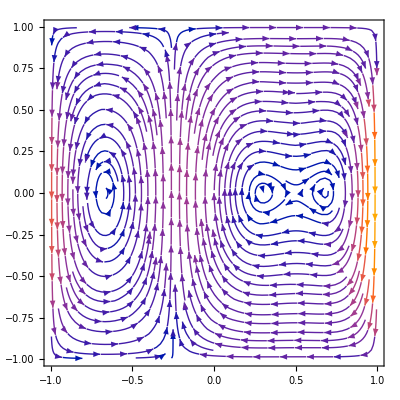

```mathematica
StreamPlot[dgsnapshot[0,{x,y},{-0.25,10}],{x,-1,1},{y,-1,1},StreamPoints->Fine]
```

#### Bursting

Hodgkin Huxley

Themis: Bursting with sqrt and withoutsqrt